```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->0.5,cj->U/5,U->5,t23->x t22,t22->0.3}
```

{Δ→0.5,𝒿→U/5,U→5,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

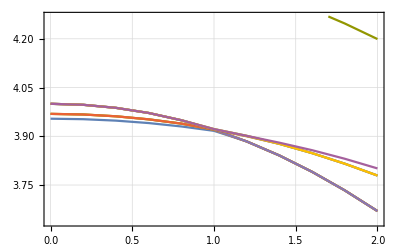

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

3.13059×10^-17

1

0.000110548

1

0.000442571

1

0.000997199

1

0.0017763

1

0.00278243

1

0.00401882

1

0.00548929

1

0.00719818

1

0.00915026

1

0.0113506

1

5.85616

1

5.82578

1

5.79224

1

5.75566

1

5.71623

1

5.67423

1

5.62997

1

5.58385

1

5.53625

1

5.48761

2

2.

2

1.99987

2

1.99947

2

1.99881

2

1.99787

2

1.99666

2

1.99515

2

1.99334

2

1.99122

2

1.98877

2

5.88332

2

5.85616

2

5.82578

2

5.79224

2

5.75566

2

5.71623

2

5.67423

2

5.62997

2

5.58385

2

5.53625

2

5.48761

3

2.

3

1.99987

3

1.99947

3

1.99881

3

1.99787

3

1.99666

3

1.99515

3

1.99334

3

1.99122

3

1.98877

3

5.88332

3

5.85616

3

5.82578

3

5.79224

3

5.75566

3

5.71623

3

5.67423

3

5.62997

3

5.58385

3

5.53625

3

5.48761

4

2.

4

1.99987

4

1.99947

4

1.99881

4

1.99787

4

1.99666

4

1.99515

4

1.99334

4

1.99122

4

1.98877

4

5.88332

4

5.85616

4

5.82578

4

5.79224

4

5.75566

4

5.71623

4

5.67423

4

5.62997

4

5.58385

4

5.53625

4

5.48761

5

6.

5

5.99897

5

5.99588

5

5.99065

5

5.98319

5

5.97337

5

5.96103

5

5.94602

5

5.92815

5

5.9073

5

5.88332

5

5.85616

5

5.82578

5

5.79224

5

5.75566

5

5.71623

5

5.67423

5

5.62997

5

5.58385

5

5.53625

5

5.48761

6

6.

6

5.99897

6

5.99588

6

5.99065

6

5.98319

6

5.97337

6

5.96103

6

5.94602

6

5.92815

6

5.9073

6

5.88332

6

0.0138046

6

0.0165174

6

1.97532

6

1.97095

6

1.96614

6

1.96085

6

1.95508

6

1.9488

6

1.94198

6

1.93462

7

6.

7

5.99897

7

5.99588

7

5.99065

7

5.98319

7

5.97337

7

5.96103

7

5.94602

7

5.92815

7

5.9073

7

1.98597

7

1.98281

7

1.97927

7

1.97532

7

1.97095

7

1.96614

7

1.96085

7

1.95508

7

1.9488

7

1.94198

7

1.93462

8

6.

8

5.99897

8

5.99588

8

5.99065

8

5.98319

8

5.97337

8

5.96103

8

5.94602

8

5.92815

8

5.9073

8

1.98597

8

1.98281

8

1.97927

8

1.97532

8

1.97095

8

1.96614

8

1.96085

8

1.95508

8

1.9488

8

1.94198

8

1.93462

9

6.

9

5.99897

9

5.99588

9

5.99065

9

5.98319

9

5.97337

9

5.96103

9

5.94602

9

5.92815

9

5.9073

9

1.98597

9

1.98281

9

1.97927

9

0.0194944

9

0.0227404

9

0.0262599

9

0.0300565

9

0.034133

9

0.0384909

9

0.0431304

9

0.0480497

10

0.75

10

0.749974

10

0.749897

10

0.74977

10

0.749592

10

0.749366

10

0.749093

10

0.748774

10

0.748412

10

0.748009

10

0.747568

10

0.747091

10

0.746581

10

0.746041

10

0.745475

10

0.744886

10

0.744276

10

0.74365

10

0.743011

10

0.742361

10

0.741705

```mathematica
data1//MatrixForm
```

(1 | 0. | 3.13059×10^-17 | 3.9541
1 | 0.1 | 0.000110548 | 3.95373
1 | 0.2 | 0.000442571 | 3.95261
1 | 0.3 | 0.000997199 | 3.95076
1 | 0.4 | 0.0017763 | 3.94816
1 | 0.5 | 0.00278243 | 3.94482
1 | 0.6 | 0.00401882 | 3.94073
1 | 0.7 | 0.00548929 | 3.93588
1 | 0.8 | 0.00719818 | 3.93027
1 | 0.9 | 0.00915026 | 3.92389
1 | 1. | 0.0113506 | 3.91675
1 | 1.1 | 5.85616 | 3.9031
1 | 1.2 | 5.82578 | 3.88415
1 | 1.3 | 5.79224 | 3.86344
1 | 1.4 | 5.75566 | 3.84095
1 | 1.5 | 5.71623 | 3.81669
1 | 1.6 | 5.67423 | 3.79068
1 | 1.7 | 5.62997 | 3.76295
1 | 1.8 | 5.58385 | 3.73352
1 | 1.9 | 5.53625 | 3.70246
1 | 2. | 5.48761 | 3.6698
2 | 0. | 2. | 3.96897
2 | 0.1 | 1.99987 | 3.9685
2 | 0.2 | 1.99947 | 3.9671
2 | 0.3 | 1.99881 | 3.96477
2 | 0.4 | 1.99787 | 3.9615
2 | 0.5 | 1.99666 | 3.9573
2 | 0.6 | 1.99515 | 3.95216
2 | 0.7 | 1.99334 | 3.94607
2 | 0.8 | 1.99122 | 3.93904
2 | 0.9 | 1.98877 | 3.93105
2 | 1. | 5.88332 | 3.92028
2 | 1.1 | 5.85616 | 3.9031
2 | 1.2 | 5.82578 | 3.88415
2 | 1.3 | 5.79224 | 3.86344
2 | 1.4 | 5.75566 | 3.84095
2 | 1.5 | 5.71623 | 3.81669
2 | 1.6 | 5.67423 | 3.79068
2 | 1.7 | 5.62997 | 3.76295
2 | 1.8 | 5.58385 | 3.73352
2 | 1.9 | 5.53625 | 3.70246
2 | 2. | 5.48761 | 3.6698
3 | 0. | 2. | 3.96897
3 | 0.1 | 1.99987 | 3.9685
3 | 0.2 | 1.99947 | 3.9671
3 | 0.3 | 1.99881 | 3.96477
3 | 0.4 | 1.99787 | 3.9615
3 | 0.5 | 1.99666 | 3.9573
3 | 0.6 | 1.99515 | 3.95216
3 | 0.7 | 1.99334 | 3.94607
3 | 0.8 | 1.99122 | 3.93904
3 | 0.9 | 1.98877 | 3.93105
3 | 1. | 5.88332 | 3.92028
3 | 1.1 | 5.85616 | 3.9031
3 | 1.2 | 5.82578 | 3.88415
3 | 1.3 | 5.79224 | 3.86344
3 | 1.4 | 5.75566 | 3.84095
3 | 1.5 | 5.71623 | 3.81669
3 | 1.6 | 5.67423 | 3.79068
3 | 1.7 | 5.62997 | 3.76295
3 | 1.8 | 5.58385 | 3.73352
3 | 1.9 | 5.53625 | 3.70246
3 | 2. | 5.48761 | 3.6698
4 | 0. | 2. | 3.96897
4 | 0.1 | 1.99987 | 3.9685
4 | 0.2 | 1.99947 | 3.9671
4 | 0.3 | 1.99881 | 3.96477
4 | 0.4 | 1.99787 | 3.9615
4 | 0.5 | 1.99666 | 3.9573
4 | 0.6 | 1.99515 | 3.95216
4 | 0.7 | 1.99334 | 3.94607
4 | 0.8 | 1.99122 | 3.93904
4 | 0.9 | 1.98877 | 3.93105
4 | 1. | 5.88332 | 3.92028
4 | 1.1 | 5.85616 | 3.9031
4 | 1.2 | 5.82578 | 3.88415
4 | 1.3 | 5.79224 | 3.86344
4 | 1.4 | 5.75566 | 3.84095
4 | 1.5 | 5.71623 | 3.81669
4 | 1.6 | 5.67423 | 3.79068
4 | 1.7 | 5.62997 | 3.76295
4 | 1.8 | 5.58385 | 3.73352
4 | 1.9 | 5.53625 | 3.70246
4 | 2. | 5.48761 | 3.6698
5 | 0. | 6. | 4.
5 | 0.1 | 5.99897 | 3.99922
5 | 0.2 | 5.99588 | 3.99689
5 | 0.3 | 5.99065 | 3.993
5 | 0.4 | 5.98319 | 3.98752
5 | 0.5 | 5.97337 | 3.98045
5 | 0.6 | 5.96103 | 3.97176
5 | 0.7 | 5.94602 | 3.96143
5 | 0.8 | 5.92815 | 3.94942
5 | 0.9 | 5.9073 | 3.93571
5 | 1. | 5.88332 | 3.92028
5 | 1.1 | 5.85616 | 3.9031
5 | 1.2 | 5.82578 | 3.88415
5 | 1.3 | 5.79224 | 3.86344
5 | 1.4 | 5.75566 | 3.84095
5 | 1.5 | 5.71623 | 3.81669
5 | 1.6 | 5.67423 | 3.79068
5 | 1.7 | 5.62997 | 3.76295
5 | 1.8 | 5.58385 | 3.73352
5 | 1.9 | 5.53625 | 3.70246
5 | 2. | 5.48761 | 3.6698
6 | 0. | 6. | 4.
6 | 0.1 | 5.99897 | 3.99922
6 | 0.2 | 5.99588 | 3.99689
6 | 0.3 | 5.99065 | 3.993
6 | 0.4 | 5.98319 | 3.98752
6 | 0.5 | 5.97337 | 3.98045
6 | 0.6 | 5.96103 | 3.97176
6 | 0.7 | 5.94602 | 3.96143
6 | 0.8 | 5.92815 | 3.94942
6 | 0.9 | 5.9073 | 3.93571
6 | 1. | 5.88332 | 3.92028
6 | 1.1 | 0.0138046 | 3.90882
6 | 1.2 | 0.0165174 | 3.90011
6 | 1.3 | 1.97532 | 3.88952
6 | 1.4 | 1.97095 | 3.87671
6 | 1.5 | 1.96614 | 3.86292
6 | 1.6 | 1.96085 | 3.84815
6 | 1.7 | 1.95508 | 3.83239
6 | 1.8 | 1.9488 | 3.81564
6 | 1.9 | 1.94198 | 3.79789
6 | 2. | 1.93462 | 3.77914
7 | 0. | 6. | 4.
7 | 0.1 | 5.99897 | 3.99922
7 | 0.2 | 5.99588 | 3.99689
7 | 0.3 | 5.99065 | 3.993
7 | 0.4 | 5.98319 | 3.98752
7 | 0.5 | 5.97337 | 3.98045
7 | 0.6 | 5.96103 | 3.97176
7 | 0.7 | 5.94602 | 3.96143
7 | 0.8 | 5.92815 | 3.94942
7 | 0.9 | 5.9073 | 3.93571
7 | 1. | 1.98597 | 3.92211
7 | 1.1 | 1.98281 | 3.91221
7 | 1.2 | 1.97927 | 3.90135
7 | 1.3 | 1.97532 | 3.88952
7 | 1.4 | 1.97095 | 3.87671
7 | 1.5 | 1.96614 | 3.86292
7 | 1.6 | 1.96085 | 3.84815
7 | 1.7 | 1.95508 | 3.83239
7 | 1.8 | 1.9488 | 3.81564
7 | 1.9 | 1.94198 | 3.79789
7 | 2. | 1.93462 | 3.77914
8 | 0. | 6. | 4.
8 | 0.1 | 5.99897 | 3.99922
8 | 0.2 | 5.99588 | 3.99689
8 | 0.3 | 5.99065 | 3.993
8 | 0.4 | 5.98319 | 3.98752
8 | 0.5 | 5.97337 | 3.98045
8 | 0.6 | 5.96103 | 3.97176
8 | 0.7 | 5.94602 | 3.96143
8 | 0.8 | 5.92815 | 3.94942
8 | 0.9 | 5.9073 | 3.93571
8 | 1. | 1.98597 | 3.92211
8 | 1.1 | 1.98281 | 3.91221
8 | 1.2 | 1.97927 | 3.90135
8 | 1.3 | 1.97532 | 3.88952
8 | 1.4 | 1.97095 | 3.87671
8 | 1.5 | 1.96614 | 3.86292
8 | 1.6 | 1.96085 | 3.84815
8 | 1.7 | 1.95508 | 3.83239
8 | 1.8 | 1.9488 | 3.81564
8 | 1.9 | 1.94198 | 3.79789
8 | 2. | 1.93462 | 3.77914
9 | 0. | 6. | 4.
9 | 0.1 | 5.99897 | 3.99922
9 | 0.2 | 5.99588 | 3.99689
9 | 0.3 | 5.99065 | 3.993
9 | 0.4 | 5.98319 | 3.98752
9 | 0.5 | 5.97337 | 3.98045
9 | 0.6 | 5.96103 | 3.97176
9 | 0.7 | 5.94602 | 3.96143
9 | 0.8 | 5.92815 | 3.94942
9 | 0.9 | 5.9073 | 3.93571
9 | 1. | 1.98597 | 3.92211
9 | 1.1 | 1.98281 | 3.91221
9 | 1.2 | 1.97927 | 3.90135
9 | 1.3 | 0.0194944 | 3.8906
9 | 1.4 | 0.0227404 | 3.88029
9 | 1.5 | 0.0262599 | 3.86916
9 | 1.6 | 0.0300565 | 3.85722
9 | 1.7 | 0.034133 | 3.84445
9 | 1.8 | 0.0384909 | 3.83084
9 | 1.9 | 0.0431304 | 3.81639
9 | 2. | 0.0480497 | 3.80109
10 | 0. | 0.75 | 4.454
10 | 0.1 | 0.749974 | 4.45336
10 | 0.2 | 0.749897 | 4.45142
10 | 0.3 | 0.74977 | 4.4482
10 | 0.4 | 0.749592 | 4.44369
10 | 0.5 | 0.749366 | 4.43789
10 | 0.6 | 0.749093 | 4.43081
10 | 0.7 | 0.748774 | 4.42244
10 | 0.8 | 0.748412 | 4.4128
10 | 0.9 | 0.748009 | 4.40188
10 | 1. | 0.747568 | 4.3897
10 | 1.1 | 0.747091 | 4.37624
10 | 1.2 | 0.746581 | 4.36153
10 | 1.3 | 0.746041 | 4.34556
10 | 1.4 | 0.745475 | 4.32835
10 | 1.5 | 0.744886 | 4.30989
10 | 1.6 | 0.744276 | 4.2902
10 | 1.7 | 0.74365 | 4.26927
10 | 1.8 | 0.743011 | 4.24713
10 | 1.9 | 0.742361 | 4.22378
10 | 2. | 0.741705 | 4.19922)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;11,1;;4]];
tmp02 = data1[[117;;118,1;;4]];
tmp03 = data1[[182;;189,1;;4]];
tmp04=Flatten[{tmp01,tmp02,tmp03},1];
e0data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[22;;31,1;;4]];
tmp02 = data1[[158;;168, 1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e1data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[85;;105,1;;4]];
tmp03=Flatten[{tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 3.9541 | 3.13059×10^-17
0.1 | 3.95373 | 0.000110548
0.2 | 3.95261 | 0.000442571
0.3 | 3.95076 | 0.000997199
0.4 | 3.94816 | 0.0017763
0.5 | 3.94482 | 0.00278243
0.6 | 3.94073 | 0.00401882
0.7 | 3.93588 | 0.00548929
0.8 | 3.93027 | 0.00719818
0.9 | 3.92389 | 0.00915026
1. | 3.91675 | 0.0113506
1.1 | 3.90882 | 0.0138046
1.2 | 3.90011 | 0.0165174
1.3 | 3.8906 | 0.0194944
1.4 | 3.88029 | 0.0227404
1.5 | 3.86916 | 0.0262599
1.6 | 3.85722 | 0.0300565
1.7 | 3.84445 | 0.034133
1.8 | 3.83084 | 0.0384909
1.9 | 3.81639 | 0.0431304
2. | 3.80109 | 0.0480497)

(0. | 3.96897 | 2.
0.1 | 3.9685 | 1.99987
0.2 | 3.9671 | 1.99947
0.3 | 3.96477 | 1.99881
0.4 | 3.9615 | 1.99787
0.5 | 3.9573 | 1.99666
0.6 | 3.95216 | 1.99515
0.7 | 3.94607 | 1.99334
0.8 | 3.93904 | 1.99122
0.9 | 3.93105 | 1.98877
1. | 3.92211 | 1.98597
1.1 | 3.91221 | 1.98281
1.2 | 3.90135 | 1.97927
1.3 | 3.88952 | 1.97532
1.4 | 3.87671 | 1.97095
1.5 | 3.86292 | 1.96614
1.6 | 3.84815 | 1.96085
1.7 | 3.83239 | 1.95508
1.8 | 3.81564 | 1.9488
1.9 | 3.79789 | 1.94198
2. | 3.77914 | 1.93462)

(0. | 4. | 6.
0.1 | 3.99922 | 5.99897
0.2 | 3.99689 | 5.99588
0.3 | 3.993 | 5.99065
0.4 | 3.98752 | 5.98319
0.5 | 3.98045 | 5.97337
0.6 | 3.97176 | 5.96103
0.7 | 3.96143 | 5.94602
0.8 | 3.94942 | 5.92815
0.9 | 3.93571 | 5.9073
1. | 3.92028 | 5.88332
1.1 | 3.9031 | 5.85616
1.2 | 3.88415 | 5.82578
1.3 | 3.86344 | 5.79224
1.4 | 3.84095 | 5.75566
1.5 | 3.81669 | 5.71623
1.6 | 3.79068 | 5.67423
1.7 | 3.76295 | 5.62997
1.8 | 3.73352 | 5.58385
1.9 | 3.70246 | 5.53625
2. | 3.6698 | 5.48761)

```mathematica
|
```

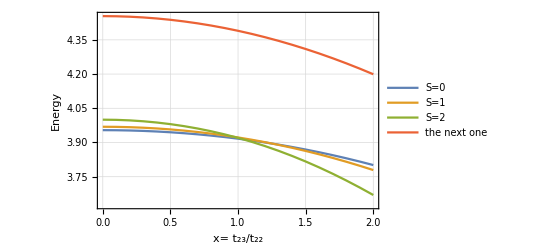

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

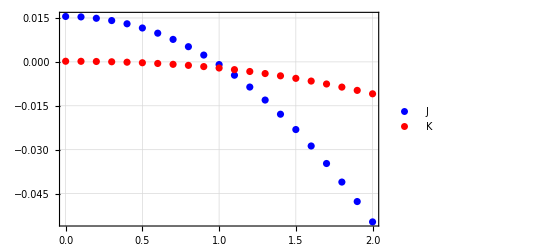

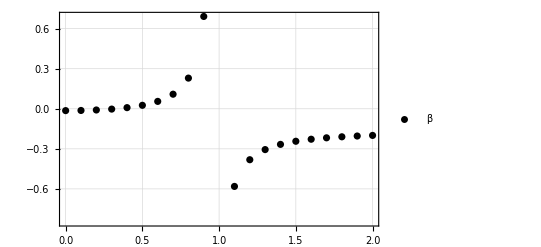

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```